# Numerical range visualization

## Initialization

```mathematica
DirectSum[A_, B_] := ArrayFlatten[{{A,0},{0,B}}];
```

Zadana je matrica A i treba nacrtati njenu numeričku sliku, tj. skup \{ <A x, x> : \|x\| = 1 \}. To možemo naivno napraviti tako da uzmemo puno slučajno odabranih x-eva i za njih nacrtamo <A x, x>.

```mathematica
NRVisualRandom[A_, Niter_:1000] := Module[{x, i, m, n, points, a},
{m, n} = Dimensions[A]; points = {};
a = Norm[A];
For[i = 0, i < Niter, ++i,
x = {RandomComplex[{-1-I, 1+I},n]};  x = ConjugateTranspose[x]/Norm[x];
AppendTo[points, Flatten[ConjugateTranspose[x].A.x][[1]]];
];
ListPlot[{Re[#], Im[#]} & /@ points, PlotRange->{{-a, a}, {-a, a}}, AspectRatio->1]
]
```

Postoji i bolji algoritam jer možemo iskoristiti činjenicu da je numerička slika konveksan skup. Također, numerička slika hermitskog operatora je segment između njegove minimalne i maksimalne svojstvene vrijednosti. Ideja algoritma za skiciranje numeričke slike je da rotiramo operator i skiciramo numeričku sliku njegovog hermitskog dijela H(e^iθA) za više odabranih kuteva θ.

Algoritam:
1. Odaberimo 0 = θ_1< θ_2 < ... < θ_p < θ_(p+1) = 2π
2. Za j = 1, ..., p ponavljamo
	(i) izračunamo maksimalnu svojstvenu vrijednost λ_j operatora H(e^iθ_jA)
	(ii) izračunamo jedinični vektor x_j koji odgovara svojstvenoj vrijednosti λ_j
	(iii) izračunamo j-ti vrh poligona Q, q_j = x_j^*A x_j
	(iv) izračunamo j-ti vrh poligona P, p_j = e^-iθ_j[ λ_j (λ_θ_j cos(θ_(j+1)-θ_j) - λ_(θ_(j+1)))/(sin(θ_(j+1)-θ_j))].
3. Stavimo p_(p+1)=p_1i q_(p+1)=q_1 i izračunamo razliku površina 
E = površina(P)-površina(Q)
4. Ako je E ‘dovoljno mali’, onda nacrtamo P. Ako ne, idemo na korak 1 i odaberemo finiju particiju.

```mathematica
polygonArea[P_] := 1/2*Im[Sum[Conjugate[P[[j]]]*P[[j+1]], {j, 1, Length[P]-1}]];
ComplexToReals[z_] := {Re[z], Im[z]};
NumericalRange[C_, eps_:10^-2] :=
Module[{a, A, pos, j, k, sys, eigen, eigenx, m, n, H, l, x, y, P, Q, f, z, e, r, d, B}, 
{m, n} = Dimensions[C];
a = Re[N[Norm[C]]];
A = 1/a*C;
e = 1; r = 2; 
While[e > eps, 
P = {}; Q = {}; 
r = 2*r;
d = 2*Pi/r;
l = {}; x = {};
For[k = 1, k≤ r, ++k ,
B = Exp[I*k*d]*A;
H = (B+ConjugateTranspose[B])/2;
{eigen, eigenx} = Eigensystem[H];
eigen = Re[eigen];
For[j = 1, j ≤ n, j++,
If[eigen[[j]] == Max[eigen], 
pos = j;
]
];
AppendTo[l, N[eigen[[pos]]]];
y = ArrayReshape[eigenx[[pos]], {n, 1}];
y = y/Norm[y];
AppendTo[x,N[y]];
];
AppendTo[l ,l[[1]]];
For[k = 1, k ≤ r, ++k,
z = (ConjugateTranspose[x[[k]]].A.x[[k]])[[1]][[1]];
AppendTo[P, N[z]];
f = (l[[k]]*Cos[d]-l[[k+1]])/Sin[d];
z = ( Cos[k*d] - I*Sin[k*d] )*(l[[k]] + I*f);
AppendTo[Q, N[z]];
];
AppendTo[P, P[[1]]];
AppendTo[Q, Q[[1]]];
e = Abs[polygonArea[Q]] - Abs[polygonArea[P]];
(*Print[P];*)
];
a*P
];
NumericalRangeVisual[A_, eps_:10^-2] := Module[{a},
a = Re[N[Norm[A]]];
Graphics[{Opacity[0.3, Blue], Polygon[ComplexToReals /@ NumericalRange[A, eps]]}, Axes->True,PlotRange->{{-a, a}, {-a, a}}, AspectRatio->1]
];
```

## Examples

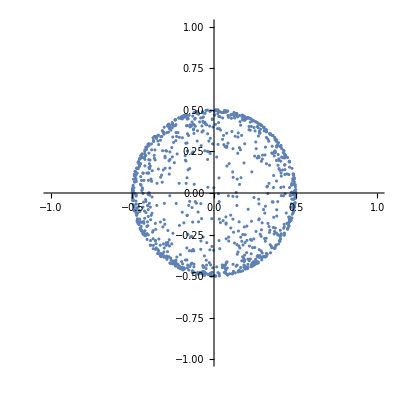

```mathematica
A = {{0, 1}, {0, 0}}; 
NRVisualRandom[A]
```

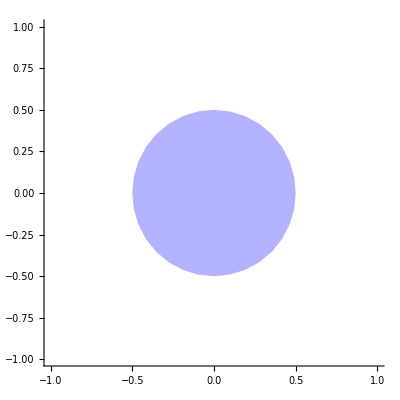

```mathematica
NumericalRangeVisual[A]
```

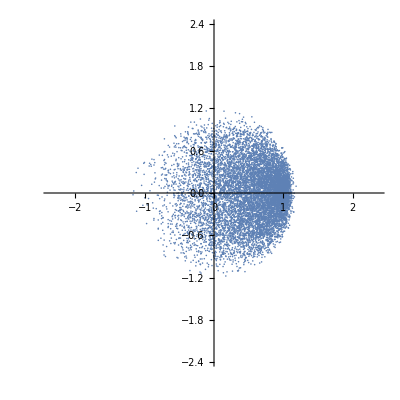

```mathematica
B = {{0, 0, 2, 1}, {0, 1, 0, 0}, {0, 0, 0, -1}, {0, 0, 0, 1}}; NRVisualRandom[B, 10000]
```

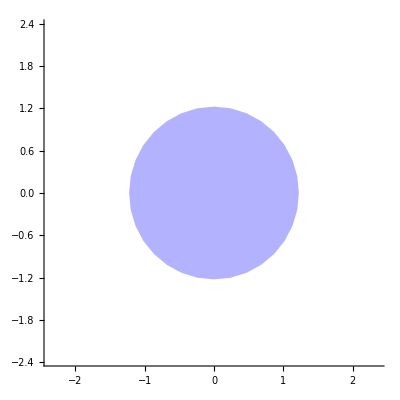

```mathematica
NumericalRangeVisual[B]
```

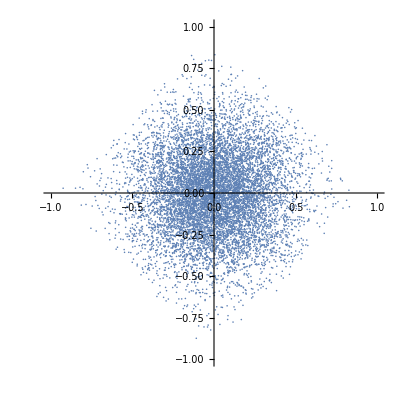

```mathematica
A3 = {{1, 0, 0, 0}, {0, I, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -I}}; NRVisualRandom[A3, 10000]
```

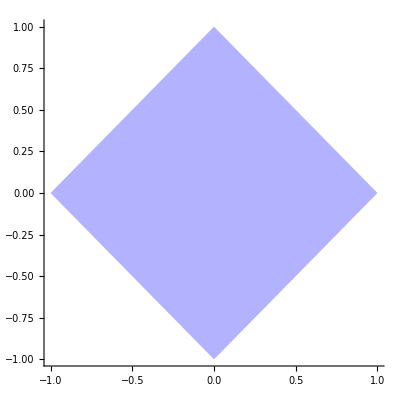

```mathematica
NumericalRangeVisual[A3]
```

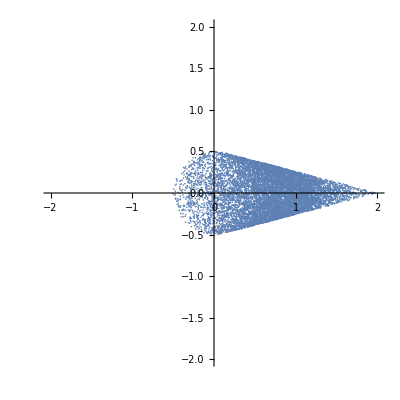

```mathematica
A4 = {{0, 1, 0}, {0, 0, 0}, {0, 0, 2}}; NRVisualRandom[A4, 10000]
```

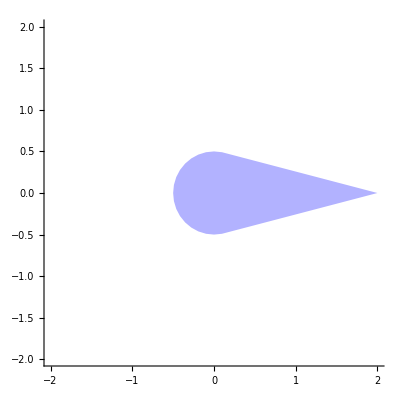

```mathematica
NumericalRangeVisual[A4, 0.1]
```

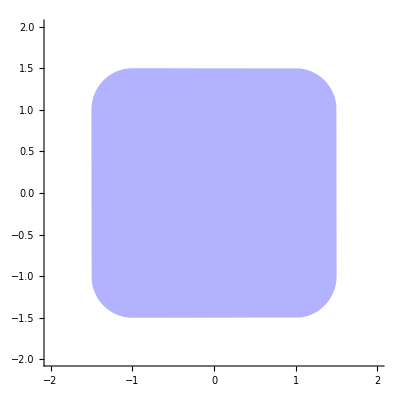

```mathematica
NumericalRangeVisual[DirectSum[DirectSum[{{1+I, 1}, {0, 1+I}}, {{-1-I, 1}, {0, -1-I}}], DirectSum[{{1-I, 1}, {0, 1-I}}, {{-1+I, 1}, {0, -1+I}}]]]
```

Ako je H hermitska matrica i a, b iz C, onda je W(aH+bI) segment u kompleksnoj ravnini

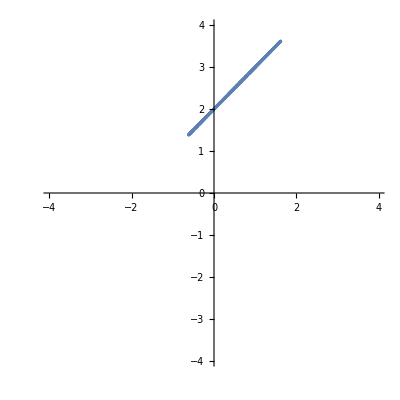

```mathematica
NRVisualRandom[
(1+I)*{{1+I, 1},
{1, 2+I}}
]
```

Jordanova dekompozicija i numerička slika

```mathematica
A = {{27,48,81},{-6,0,0},{1,0,3}};
J = JordanDecomposition[A][[2]];
```

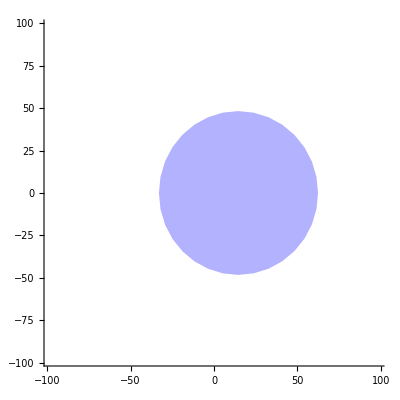

```mathematica
NumericalRangeVisual[A]
```

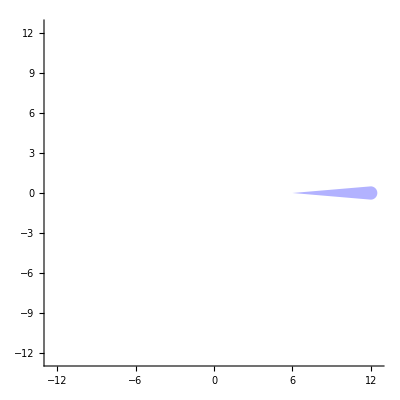

```mathematica
NumericalRangeVisual[J]
```

Numerička slika Jordanove klijetke (dijagonalni elementi realiziraju translaciju, veličina klijetke radijus kruga)

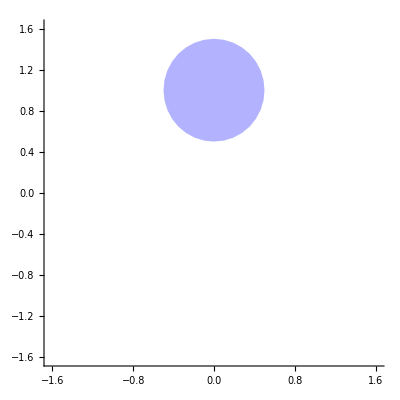

```mathematica
μ = I; k = 2;
J =SparseArray[{{i_,i_}->μ, {i_,j_}/;j==i+1->1},{k,k}];NumericalRangeVisual[J]
```

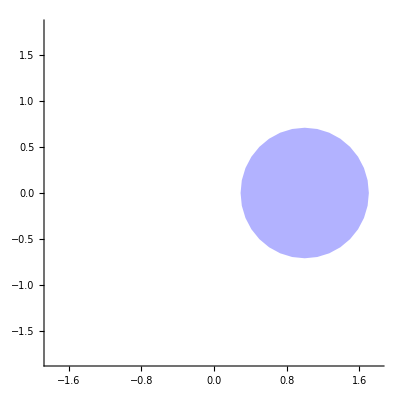

```mathematica
μ = 1; k = 3;
J =SparseArray[{{i_,i_}->μ, {i_,j_}/;j==i+1->1},{k,k}];NumericalRangeVisual[J]
```

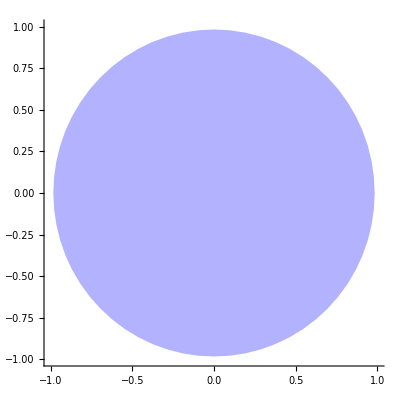

```mathematica
μ = 0; k = 16;
J =SparseArray[{{i_,i_}->μ, {i_,j_}/;j==i+1->1},{k,k}];NumericalRangeVisual[J]
```

Iz Halmosa

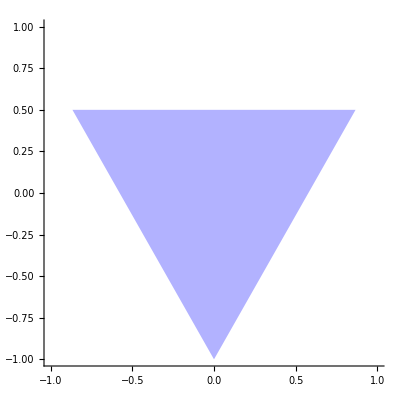

```mathematica
NumericalRangeVisual[{{0, 0, I}, {1, 0, 0}, {0, 1, 0}}]
```

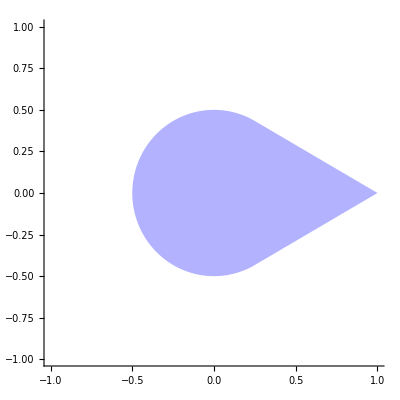

```mathematica
NumericalRangeVisual[{{0, 0, 0}, {1, 0, 0}, {0, 0, 1}}]
```

# Davis-Wielandtova ljuska

## Initialization

```mathematica
DWVisualRandom[A_, Niter_:1000] := Module[{x, i, m, n, points, a, z},
{m, n} = Dimensions[A]; points = {};
a = Norm[A];
For[i = 0, i < Niter, ++i,
x = {RandomComplex[{-1-I, 1+I},n]};
x = ConjugateTranspose[x]/Norm[x];
z = Flatten[ConjugateTranspose[x].A.x][[1]];
AppendTo[points, {Re[z], Im[z], Norm[A.x]^2}];
];
ListPointPlot3D[points, PlotRange->{{-a, a}, {-a, a}, {0, a^2}}, AspectRatio->1, ColorFunction->"Rainbow"]
]
```

```mathematica
DWVisualRandomDensity[A_, Niter_:1000] := Module[{x, i, m, n, points, a, z},
{m, n} = Dimensions[A]; points = {};
a = Norm[A];
For[i = 0, i < Niter, ++i,
x = {RandomComplex[{-1-I, 1+I},n]};
x = ConjugateTranspose[x]/Norm[x];
z = Flatten[ConjugateTranspose[x].A.x][[1]];
AppendTo[points, {Re[z], Im[z], Norm[A.x]^2}];
];
ListDensityPlot[points]
]
```

```mathematica
DWVisualRandomConvex[A_, Niter_:1000] := Module[{x, i, m, n, points, a, z},
{m, n} = Dimensions[A]; points = {};
a = Norm[A];
For[i = 0, i < Niter, ++i,
x = {RandomComplex[{-1-I, 1+I},n]};
x = ConjugateTranspose[x]/Norm[x];
z = Flatten[ConjugateTranspose[x].A.x][[1]];
AppendTo[points, {Re[z], Im[z], Norm[A.x]^2}];
];
ConvexHullMesh[points]
]
```

## Examples

DW shell of a normal matrix in M_ 2 with eigenvalues a_1, a_2 is a line segment connecting (a_1, |a_1|^2) and (a_2, |a_2|^2)

```mathematica
Show[DWVisualRandom[{{1, 0}, {0, 2}}], Graphics3D[{PointSize[0.025],Point[{1,0, 1}], Point[{2,0, 4}]}]]
```

-Graphics3D-

```mathematica
Show[DWVisualRandom[{{1+I, 0}, {0, 2I}}], Graphics3D[{PointSize[0.025],Point[{1,1, 2}], Point[{0,2, 4}]}]]
```

-Graphics3D-

A direct sum of normal matrices

```mathematica
DWVisualRandom[{
{0, 1, 0, 0}, 
{1, 0, 0, 0}, 
{0, 0, 0, I},
{0, 0, I, 0}
}, 10000]
```

-Graphics3D-

An M_ 2 matrix which is not normal

```mathematica
DWVisualRandom[{
{1, I}, 
{I, -1}
}, 10000]
```

-Graphics3D-

Example of an isometry

```mathematica
t = π/6;
R = {
{Cos[t], -Sin[t], 0, 0},
{Sin[t], Cos[t], 0, 0},
{0, 0, 0, 1},
{0, 0, 1, 0}
};
DWVisualRandom[R, 10000]
```

-Graphics3D-

Example from the article

```mathematica
A= {{0, 0, 2, 1}, 
{0, 1, 0, 0}, 
{0, 0, 0, -1}, 
{0, 0, 0, 1}};
```

```mathematica
g = DWVisualRandom[{
{0, 0, 2, 1}, 
{0, 1, 0, 0}, 
{0, 0, 0, -1}, 
{0, 0, 0, 1}
}, 20000];
```

```mathematica
Show[g, Graphics3D[{PointSize[0.05], Point[{0, 0, 5}]}]]
```

-Graphics3D-

```mathematica
Show[g, Graphics3D[{Opacity[0.2, Yellow],Ellipsoid[{0, 0, 3}, {2, 1, 2.4}]}], BoxRatios -> {1, 1, 1}, AspectRatio -> 1]
```

-Graphics3D-

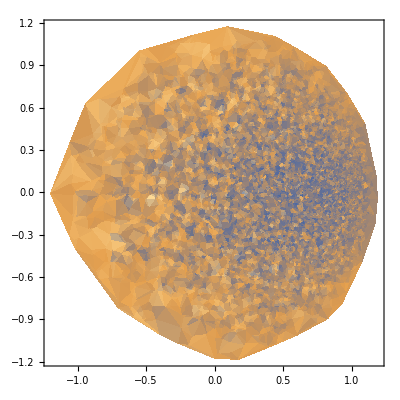

```mathematica
DWVisualRandomDensity[A, 10000]
```

```mathematica
Show[DWVisualRandomConvex[A, 10000], Graphics3D[ { Red, Thick, Line[{{0, 0, -2}, {0, 0, 7}}] } ]]
```

-Graphics3D-

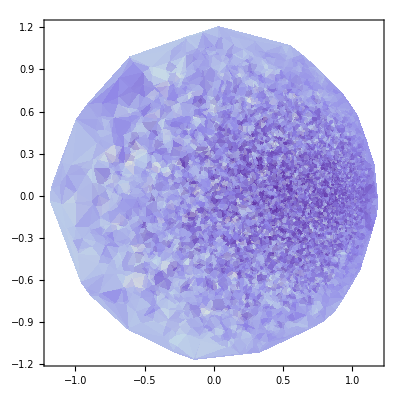

```mathematica
DWVisualRandomDensity[A, 10000]
```

```mathematica
Show[DWVisualRandom[A, 10000], Graphics3D[{PointSize[0.025], Point[{0, 0, Norm[A]^2}]}]]
```

-Graphics3D-